# Neighbourhood analyses including ICM composition scatter plots for the simulation data

## Supplementary material for Fischer et al "The salt-and-pepper pattern in mouse blastocysts is compatible with signalling beyond the nearest neighbours."

## Initialisation

```mathematica
baseFolderSimulations=StringReplace[NotebookDirectory[],"analysisCode"->("dataPreProcessing\\"<>"simulations")];
```

```mathematica
fontOption="Arial";
```

```mathematica
calcPlotRatioSortedByCellNumber[exprCell_,exprNeigh_,comp_,stages_,cellNumberPerEmbryo_,fateExcluded_:"TE"]:=Block[{cellPosPosNeighPropAll,numNeigh,cellNumbers,numPosCells,numNegCells,cellNegNegNeighPropAll,plotRatios},
cellPosPosNeighPropAll=Select[#,NumberQ]&/@Table[If[(numNeigh=Length[Select[#,#[[1]]≠fateExcluded&]])>0,Count[Select[#,#[[1]]≠fateExcluded&][[All,2]],z_/;StringContainsQ[z,exprNeigh<>"+"]]/numNeigh,"NA"]&/@(Select[comp[[i,2]],#[[1,1]]≠fateExcluded&&StringContainsQ[#[[1,2]],exprCell<>"+"]&][[All,2,All,2;;3]]),{i,1,Length[comp]}];
cellNumbers=Table[Length[Select[comp[[i,2]],#[[1,1]]≠fateExcluded&]],{i,1,Length[comp]}];
numPosCells=Table[Count[Select[comp[[i,2]],#[[1,1]]≠fateExcluded&][[All,1,2]],z_/;StringContainsQ[z,exprNeigh<>"+"]],{i,1,Length[comp]}];
numNegCells=Table[Count[Select[comp[[i,2]],#[[1,1]]≠fateExcluded&][[All,1,2]],z_/;StringContainsQ[z,exprNeigh<>"-"]],{i,1,Length[comp]}];
cellNegNegNeighPropAll=Select[#,NumberQ]&/@Table[If[(numNeigh=Length[Select[#,#[[1]]≠fateExcluded&]])>0,Count[Select[#,#[[1]]≠fateExcluded&][[All,2]],z_/;StringContainsQ[z,exprNeigh<>"-"]]/numNeigh,"NA"]&/@(Select[comp[[i,2]],#[[1,1]]≠fateExcluded&&StringContainsQ[#[[1,2]],exprNeigh<>"-"]&][[All,2,All,2;;3]]),{i,1,Length[comp]}];
plotRatios=MapThread[Rule,{{"Stage","CellNumberEmbryo","CellNumberICM","NumPosCellsICM","NumNegCellsICM","MeanRatioNegNeighbNegCell","SEMRatioNegNeighbNegCell","MeanRatioPosNeighbPosCell","SEMRatioPosNeighbPosCell"},#}]&/@Table[{stages[[i]],cellNumberPerEmbryo[[i]],cellNumbers[[i]],numPosCells[[i]],numNegCells[[i]],Mean[cellNegNegNeighPropAll[[i]]],If[Length[cellNegNegNeighPropAll[[i]]]>1,(StandardDeviation[cellNegNegNeighPropAll[[i]]]/Sqrt[Length[cellNegNegNeighPropAll[[i]]]]),0],
Mean[cellPosPosNeighPropAll[[i]]],If[Length[cellPosPosNeighPropAll[[i]]]>1,(StandardDeviation[cellPosPosNeighPropAll[[i]]]/Sqrt[Length[cellPosPosNeighPropAll[[i]]]]),0]},{i,1,Length[cellNumbers]}];
SortBy[plotRatios,"CellNumber"/.#&]
]
```

```mathematica
calcPlotRatioAllCells[exprCell_,exprNeigh_,comp_,stages_,cellNumberPerEmbryo_,fateExcluded_:"TE"]:=Block[{cellPosPosNeighPropAll,numNeigh,cells,cellNumbers,cellNegNegNeighPropAll,plotRatios,numPosCells,numNegCells,centroids,distancesToCentroids},
cellPosPosNeighPropAll=Select[#,NumberQ]&/@Table[If[(numNeigh=Length[Select[#,#[[1]]≠fateExcluded&]])>0,Count[Select[#,#[[1]]≠fateExcluded&][[All,2]],z_/;StringContainsQ[z,exprNeigh<>"+"]]/numNeigh,"NA"]&/@(Select[comp[[i,2]],#[[1,1]]≠fateExcluded&&StringContainsQ[#[[1,2]],exprCell<>"+"]&][[All,2,All,2;;3]]),{i,1,Length[comp]}];
cellNumbers=Table[Length[Select[comp[[i,2]],#[[1,1]]≠fateExcluded&]],{i,1,Length[comp]}];
numPosCells=Table[Count[Select[comp[[i,2]],#[[1,1]]≠fateExcluded&][[All,1,2]],z_/;StringContainsQ[z,exprNeigh<>"+"]],{i,1,Length[comp]}];
numNegCells=Table[Count[Select[comp[[i,2]],#[[1,1]]≠fateExcluded&][[All,1,2]],z_/;StringContainsQ[z,exprNeigh<>"-"]],{i,1,Length[comp]}];
cellNegNegNeighPropAll=Select[#,NumberQ]&/@Table[If[(numNeigh=Length[Select[#,#[[1]]≠fateExcluded&]])>0,Count[Select[#,#[[1]]≠fateExcluded&][[All,2]],z_/;StringContainsQ[z,exprNeigh<>"-"]]/numNeigh,"NA"]&/@(Select[comp[[i,2]],#[[1,1]]≠fateExcluded&&StringContainsQ[#[[1,2]],exprNeigh<>"-"]&][[All,2,All,2;;3]]),{i,1,Length[comp]}];
MapThread[Rule,{{"Stage","CellNumberEmbryo","CellNumberICM","NumPosCellsICM","NumNegCellsICM","RatiosNegNeighbNegCell","RatiosPosNeighbPosCell"},#}]&/@Table[{stages[[i]],cellNumberPerEmbryo[[i]],cellNumbers[[i]],numPosCells[[i]],numNegCells[[i]],cellNegNegNeighPropAll[[i]],cellPosPosNeighPropAll[[i]]},{i,1,Length[cellNumbers]}]
]
```

```mathematica
calcDistances[comp_,exprCell_]:=Block[{cells,centroids,maxDistanceToCentroid,distancesToCentroids,distancesPositive,distancesNegative},
cells=Table[Select[comp[[i,2,All,1]],#[[1]]≠"TE"&],{i,1,Length[comp]}];
centroids=Mean[#[[All,3]]]&/@cells;
distancesToCentroids=Table[EuclideanDistance[#,centroids[[i]]]&/@cells[[i,All,3]],{i,1,Length[cells]}];
maxDistanceToCentroid=Max/@distancesToCentroids;
distancesPositive=Table[Pick[distancesToCentroids[[i]],cells[[i,All,2]],z_/;StringContainsQ[z,exprCell<>"+"]],{i,1,Length[cells]}];
distancesNegative=Table[Pick[distancesToCentroids[[i]],cells[[i,All,2]],z_/;StringContainsQ[z,exprCell<>"-"]],{i,1,Length[cells]}];
Table[{"Stage"->comp[[i,1]],"maxDistanceToCentroid"->maxDistanceToCentroid[[i]],"distancesToCentroids"->distancesToCentroids[[i]],"distancesPositive"->distancesPositive[[i]],"distancesNegative"->distancesNegative[[i]]},{i,1,Length[comp]}]
]
```

## Rule-based models: ICM composition scatter plots

### Random model with multiple replicates

#### Random model NANOG

```mathematica
nanogNanogComp=Import[FileNameJoin[{baseFolderSimulations,"Results\\nanogNanogCompRandom.mx"}]];
```

```mathematica
stages=nanogNanogComp[[All,1,3]];
```

```mathematica
cellNumberPerEmbryo=Length/@nanogNanogComp[[All,2]];
```

```mathematica
plotRatiosNAllCells=calcPlotRatioAllCells["N","N",nanogNanogComp,stages,cellNumberPerEmbryo];
```

```mathematica
plotRatiosNSortedRaw=calcPlotRatioSortedByCellNumber["N","N",nanogNanogComp,stages,cellNumberPerEmbryo];
```

```mathematica
plotRatiosNSorted=Select[plotRatiosNSortedRaw,NumberQ["MeanRatioNegNeighbNegCell"/.#]&&NumberQ["MeanRatioPosNeighbPosCell"/.#]&];
```

```mathematica
Length[plotRatiosNSortedRaw]-Length[plotRatiosNSorted]
```

315

```mathematica
plotRatiosNSortedByStage=Table[Select[plotRatiosNSorted,("Stage"/.#)==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
correlNm=N@Correlation[("NumNegCellsICM"/"CellNumberICM")/.Select[plotRatiosNSorted,("Stage"/.#)>3&],"MeanRatioNegNeighbNegCell"/.Select[plotRatiosNSorted,("Stage"/.#)>3&]]
```

0.970556

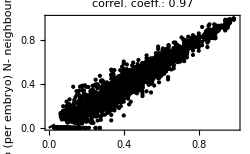

```mathematica
plotNeighbNm=Show[Graphics[{Black,Point[{("NumNegCellsICM"/"CellNumberICM"),"MeanRatioNegNeighbNegCell"}/.#]}&/@Select[plotRatiosNSorted,("Stage"/.#)>3&],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion N- in ICM","mean ratio (per embryo)\nN- neighbours of N- cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@("correl. coeff.: "<>ToString[Round[correlNm,0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbNm_Random.png"}],plotNeighbNm]
```

```mathematica
correlNp=N@Correlation[("NumPosCellsICM"/"CellNumberICM")/.Select[plotRatiosNSorted,("Stage"/.#)>3&],"MeanRatioPosNeighbPosCell"/.Select[plotRatiosNSorted,("Stage"/.#)>3&]]
```

0.979949

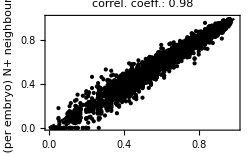

```mathematica
plotNeighbNp=Show[Graphics[{Black,Point[{("NumPosCellsICM"/"CellNumberICM"),"MeanRatioPosNeighbPosCell"}/.#]}&/@Select[plotRatiosNSorted,("Stage"/.#)>3&],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion N+ in ICM","mean ratio (per embryo)\nN+ neighbours of N+ cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@("correl. coeff.: "<>ToString[Round[correlNp,0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbNp_Random.png"}],plotNeighbNp]
```

```mathematica
correlByStageNm=Table [N@Correlation[("NumNegCellsICM"/"CellNumberICM")/.plotRatiosNSortedByStage[[i]],"MeanRatioNegNeighbNegCell"/.plotRatiosNSortedByStage[[i]]],{i,1,3}]
```

{0.96306,0.955629,0.967853}

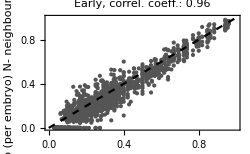
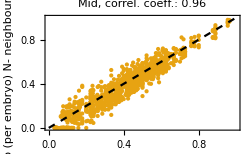
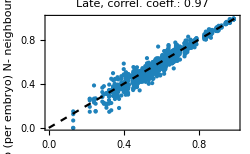

```mathematica
plotNeighbByStageNm=Row[Table[Show[Graphics[{colour3[("Stage"/.#)/.{3.5->1,4.0->2,4.5->3}],Point[{("NumNegCellsICM"/"CellNumberICM"),"MeanRatioNegNeighbNegCell"}/.#]}&/@plotRatiosNSortedByStage[[i]],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion N- in ICM","mean ratio (per embryo)\nN- neighbours of N- cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@({"Early, ","Mid, ","Late, "}[[i]]<>"correl. coeff.: "<>ToString[Round[correlByStageNm[[i]],0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbByStageNm_Random.png"}],plotNeighbByStageNm]
```

```mathematica
correlByStageNp=Table [N@Correlation[("NumPosCellsICM"/"CellNumberICM")/.plotRatiosNSortedByStage[[i]],"MeanRatioPosNeighbPosCell"/.plotRatiosNSortedByStage[[i]]],{i,1,3}]
```

{0.980595,0.971622,0.963769}

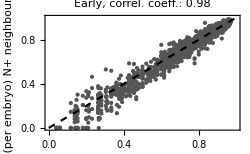
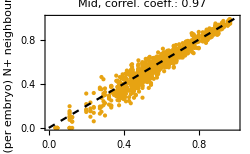
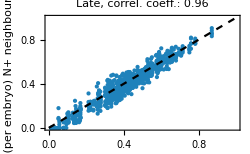

```mathematica
plotNeighbByStageNp=Row[Table[Show[Graphics[{colour3[("Stage"/.#)/.{3.5->1,4.0->2,4.5->3}],Point[{("NumPosCellsICM"/"CellNumberICM"),"MeanRatioPosNeighbPosCell"}/.#]}&/@plotRatiosNSortedByStage[[i]],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion N+ in ICM","mean ratio (per embryo)\nN+ neighbours of N+ cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@({"Early, ","Mid, ","Late, "}[[i]]<>"correl. coeff.: "<>ToString[Round[correlByStageNp[[i]],0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbByStageNp_Random.png"}],plotNeighbByStageNp]
```

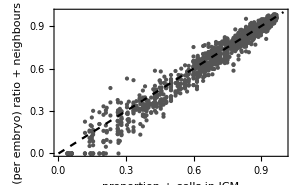

```mathematica
{propNpRandom}=Table[Show[Graphics[{colour3[("Stage"/.#)/.{3.5->1,4.0->2,4.5->3}],Point[{("NumPosCellsICM"/"CellNumberICM"),"MeanRatioPosNeighbPosCell"}/.#]}&/@plotRatiosNSortedByStage[[i]],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->300,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion + cells in ICM","mean (per embryo) ratio\n+ neighbours of + cells"})],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,1}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","propNpRandom.png"}],propNpRandom]
```

#### Random model GATA6

```mathematica
gata6Gata6Comp=Import[FileNameJoin[{baseFolderSimulations,"Results\\gata6Gata6CompRandom.mx"}]];
```

```mathematica
stages=gata6Gata6Comp[[All,1,3]];
```

```mathematica
cellNumberPerEmbryo=Length/@gata6Gata6Comp[[All,2]];
```

```mathematica
plotRatiosG6AllCells=calcPlotRatioAllCells["G6","G6",gata6Gata6Comp,stages,cellNumberPerEmbryo];
```

```mathematica
plotRatiosG6SortedRaw=calcPlotRatioSortedByCellNumber["G6","G6",gata6Gata6Comp,stages,cellNumberPerEmbryo];
```

```mathematica
plotRatiosG6Sorted=Select[plotRatiosG6SortedRaw,NumberQ["MeanRatioNegNeighbNegCell"/.#]&&NumberQ["MeanRatioPosNeighbPosCell"/.#]&];
```

```mathematica
Length[plotRatiosG6SortedRaw]-Length[plotRatiosG6Sorted]
```

501

```mathematica
plotRatiosG6SortedRawExt=Join[#,{"DiffToLineNegNeigh"->("MeanRatioNegNeighbNegCell"-("NumNegCellsICM"/"CellNumberICM"))/.#,"DiffToLinePosNeigh"->("MeanRatioPosNeighbPosCell"-("NumPosCellsICM"/"CellNumberICM"))/.#}]&/@plotRatiosG6SortedRaw;
```

```mathematica
plotRatiosG6SortedByStage=Table[Select[plotRatiosG6Sorted,("Stage"/.#)==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
correlG6m=N@Correlation[("NumNegCellsICM"/"CellNumberICM")/.Select[plotRatiosG6Sorted,("Stage"/.#)>3&],"MeanRatioNegNeighbNegCell"/.Select[plotRatiosG6Sorted,("Stage"/.#)>3&]]
```

0.952901

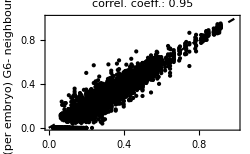

```mathematica
plotNeighbG6m=Show[Graphics[{Black,Point[{("NumNegCellsICM"/"CellNumberICM"),"MeanRatioNegNeighbNegCell"}/.#]}&/@Select[plotRatiosG6Sorted,("Stage"/.#)>3&],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion G6- in ICM","mean ratio (per embryo)\nG6- neighbours of G6- cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@("correl. coeff.: "<>ToString[Round[correlG6m,0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbG6m_Random.png"}],plotNeighbG6m]
```

```mathematica
correlG6p=N@Correlation[("NumPosCellsICM"/"CellNumberICM")/.Select[plotRatiosG6Sorted,("Stage"/.#)>3&],"MeanRatioPosNeighbPosCell"/.Select[plotRatiosG6Sorted,("Stage"/.#)>3&]]
```

0.972195

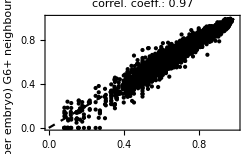

```mathematica
plotNeighbG6p=Show[Graphics[{Black,Point[{("NumPosCellsICM"/"CellNumberICM"),"MeanRatioPosNeighbPosCell"}/.#]}&/@Select[plotRatiosG6Sorted,("Stage"/.#)>3&],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion G6+ in ICM","mean ratio (per embryo)\nG6+ neighbours of G6+ cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@("correl. coeff.: "<>ToString[Round[correlG6p,0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbG6p_Random.png"}],plotNeighbG6p]
```

```mathematica
correlByStageG6m=Table [N@Correlation[("NumNegCellsICM"/"CellNumberICM")/.plotRatiosG6SortedByStage[[i]],"MeanRatioNegNeighbNegCell"/.plotRatiosG6SortedByStage[[i]]],{i,1,3}]
```

{0.964576,0.914861,0.921306}

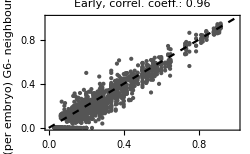
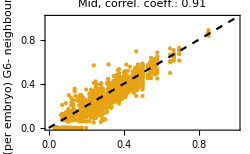
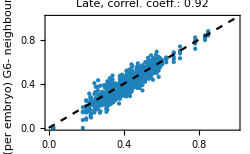

```mathematica
plotNeighbByStageG6m=Row[Table[Show[Graphics[{colour3[("Stage"/.#)/.{3.5->1,4.0->2,4.5->3}],Point[{("NumNegCellsICM"/"CellNumberICM"),"MeanRatioNegNeighbNegCell"}/.#]}&/@plotRatiosG6SortedByStage[[i]],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion G6- in ICM","mean ratio (per embryo)\nG6- neighbours of G6- cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@({"Early, ","Mid, ","Late, "}[[i]]<>"correl. coeff.: "<>ToString[Round[correlByStageG6m[[i]],0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbByStageG6m_Random.png"}],plotNeighbByStageG6m]
```

```mathematica
correlByStageG6p=Table [N@Correlation[("NumPosCellsICM"/"CellNumberICM")/.plotRatiosG6SortedByStage[[i]],"MeanRatioPosNeighbPosCell"/.plotRatiosG6SortedByStage[[i]]],{i,1,3}]
```

{0.979306,0.956688,0.945015}

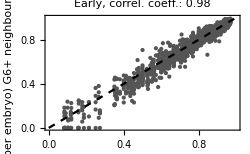
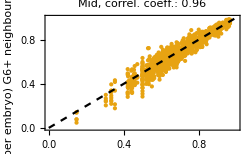
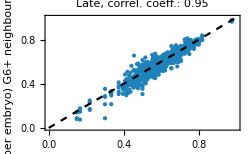

```mathematica
plotNeighbByStageG6p=Row[Table[Show[Graphics[{colour3[("Stage"/.#)/.{3.5->1,4.0->2,4.5->3}],Point[{("NumPosCellsICM"/"CellNumberICM"),"MeanRatioPosNeighbPosCell"}/.#]}&/@plotRatiosG6SortedByStage[[i]],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion G6+ in ICM","mean ratio (per embryo)\nG6+ neighbours of G6+ cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@({"Early, ","Mid, ","Late, "}[[i]]<>"correl. coeff.: "<>ToString[Round[correlByStageG6p[[i]],0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbByStageG6p_Random.png"}],plotNeighbByStageG6p]
```

#### Local cluster model p=0.55 (see also LocalClusteringScan.nb)

```mathematica
quadrantsComp=Import[FileNameJoin[{baseFolderSimulations,"Results\\quadrantsComp_LocalClust0.55.mx"}]];
```

```mathematica
stages=quadrantsComp[[All,1,3]];
```

```mathematica
cellNumberPerEmbryo=Length/@quadrantsComp[[All,2]];
```

```mathematica
plotRatiosAllCells=calcPlotRatioAllCells["","",quadrantsComp,stages,cellNumberPerEmbryo];
```

```mathematica
plotRatiosSortedRaw=calcPlotRatioSortedByCellNumber["","",quadrantsComp,stages,cellNumberPerEmbryo];
```

```mathematica
plotRatiosSorted=Select[plotRatiosSortedRaw,NumberQ["MeanRatioNegNeighbNegCell"/.#]&&NumberQ["MeanRatioPosNeighbPosCell"/.#]&];
```

```mathematica
Length[plotRatiosSortedRaw]-Length[plotRatiosSorted]
```

3

```mathematica
plotRatiosSortedRawExt=Join[#,{"DiffToLineNegNeigh"->("MeanRatioNegNeighbNegCell"-("NumNegCellsICM"/"CellNumberICM"))/.#,"DiffToLinePosNeigh"->("MeanRatioPosNeighbPosCell"-("NumPosCellsICM"/"CellNumberICM"))/.#}]&/@plotRatiosSortedRaw;
```

```mathematica
plotRatiosSortedByStage=Table[Select[plotRatiosSorted,("Stage"/.#)==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
correlM=N@Correlation[("NumNegCellsICM"/"CellNumberICM")/.Select[plotRatiosSorted,("Stage"/.#)>3&],"MeanRatioNegNeighbNegCell"/.Select[plotRatiosSorted,("Stage"/.#)>3&]]
```

0.874671

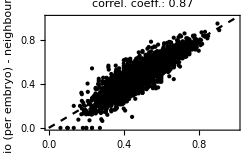

```mathematica
plotNeighbM=Show[Graphics[{Black,Point[{("NumNegCellsICM"/"CellNumberICM"),"MeanRatioNegNeighbNegCell"}/.#]}&/@Select[plotRatiosSorted,("Stage"/.#)>3&],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion - cells in ICM","mean ratio (per embryo)\n- neighbours of - cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@("correl. coeff.: "<>ToString[Round[correlM,0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbM_Cluster055.png"}],plotNeighbM]
```

```mathematica
correlP=N@Correlation[("NumPosCellsICM"/"CellNumberICM")/.Select[plotRatiosSorted,("Stage"/.#)>3&],"MeanRatioPosNeighbPosCell"/.Select[plotRatiosSorted,("Stage"/.#)>3&]]
```

0.88062

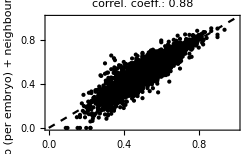

```mathematica
plotNeighbP=Show[Graphics[{Black,Point[{("NumPosCellsICM"/"CellNumberICM"),"MeanRatioPosNeighbPosCell"}/.#]}&/@Select[plotRatiosSorted,("Stage"/.#)>3&],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion + cells in ICM","mean ratio (per embryo)\n+ neighbours of + cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@("correl. coeff.: "<>ToString[Round[correlP,0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbP_Cluster055.png"}],plotNeighbP]
```

```mathematica
correlByStageM=Table [N@Correlation[("NumNegCellsICM"/"CellNumberICM")/.plotRatiosSortedByStage[[i]],"MeanRatioNegNeighbNegCell"/.plotRatiosSortedByStage[[i]]],{i,1,3}]
```

{0.872145,0.878533,0.881586}

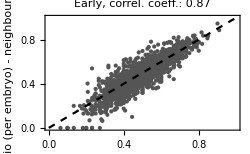
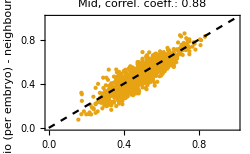
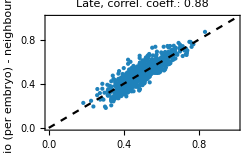

```mathematica
plotNeighbByStageM=Row[Table[Show[Graphics[{colour3[("Stage"/.#)/.{3.5->1,4.0->2,4.5->3}],Point[{("NumNegCellsICM"/"CellNumberICM"),"MeanRatioNegNeighbNegCell"}/.#]}&/@plotRatiosSortedByStage[[i]],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion - cells in ICM","mean ratio (per embryo)\n- neighbours of - cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@({"Early, ","Mid, ","Late, "}[[i]]<>"correl. coeff.: "<>ToString[Round[correlByStageM[[i]],0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbByStageM_Cluster055.png"}],plotNeighbByStageM]
```

```mathematica
correlByStageP=Table [N@Correlation[("NumPosCellsICM"/"CellNumberICM")/.plotRatiosSortedByStage[[i]],"MeanRatioPosNeighbPosCell"/.plotRatiosSortedByStage[[i]]],{i,1,3}]
```

{0.883629,0.879579,0.877974}

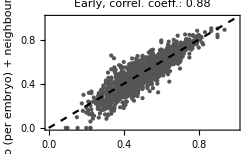
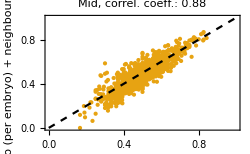
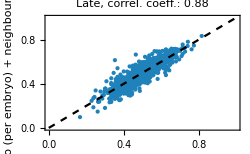

```mathematica
plotNeighbByStageP=Row[Table[Show[Graphics[{colour3[("Stage"/.#)/.{3.5->1,4.0->2,4.5->3}],Point[{("NumPosCellsICM"/"CellNumberICM"),"MeanRatioPosNeighbPosCell"}/.#]}&/@plotRatiosSortedByStage[[i]],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion + cells in ICM","mean ratio (per embryo)\n+ neighbours of + cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@({"Early, ","Mid, ","Late, "}[[i]]<>"correl. coeff.: "<>ToString[Round[correlByStageP[[i]],0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbByStageP_Cluster055.png"}],plotNeighbByStageP]
```

#### Alternating

```mathematica
nanogNanogComp=Import[FileNameJoin[{baseFolderSimulations,"Results\\nanogNanogCompNearestNeigh.mx"}]];
```

```mathematica
stages=nanogNanogComp[[All,1,3]];
```

```mathematica
cellNumberPerEmbryo=Length/@nanogNanogComp[[All,2]];
```

```mathematica
plotRatiosNAllCells=calcPlotRatioAllCells["N","N",nanogNanogComp,stages,cellNumberPerEmbryo];
```

```mathematica
plotRatiosNSortedRaw=calcPlotRatioSortedByCellNumber["N","N",nanogNanogComp,stages,cellNumberPerEmbryo];
```

```mathematica
plotRatiosNSorted=Select[plotRatiosNSortedRaw,NumberQ["MeanRatioNegNeighbNegCell"/.#]&&NumberQ["MeanRatioPosNeighbPosCell"/.#]&];
```

```mathematica
Length[plotRatiosNSortedRaw]-Length[plotRatiosNSorted]
```

0

```mathematica
plotRatiosNSortedRawExt=Join[#,{"DiffToLineNegNeigh"->("MeanRatioNegNeighbNegCell"-("NumNegCellsICM"/"CellNumberICM"))/.#,"DiffToLinePosNeigh"->("MeanRatioPosNeighbPosCell"-("NumPosCellsICM"/"CellNumberICM"))/.#}]&/@plotRatiosNSortedRaw;
```

```mathematica
plotRatiosNSortedByStage=Table[Select[plotRatiosNSorted,("Stage"/.#)==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
correlM=N@Correlation[("NumNegCellsICM"/"CellNumberICM")/.Select[plotRatiosNSorted,("Stage"/.#)>3&],"MeanRatioNegNeighbNegCell"/.Select[plotRatiosNSorted,("Stage"/.#)>3&]]
```

0.302875

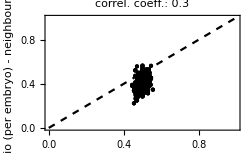

```mathematica
plotNeighbM=Show[Graphics[{Black,Point[{("NumNegCellsICM"/"CellNumberICM"),"MeanRatioNegNeighbNegCell"}/.#]}&/@Select[plotRatiosNSorted,("Stage"/.#)>3&],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion - cells in ICM","mean ratio (per embryo)\n- neighbours of - cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@("correl. coeff.: "<>ToString[Round[correlM,0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbM_Altern.png"}],plotNeighbM]
```

```mathematica
correlP=N@Correlation[("NumPosCellsICM"/"CellNumberICM")/.Select[plotRatiosNSorted,("Stage"/.#)>3&],"MeanRatioPosNeighbPosCell"/.Select[plotRatiosNSorted,("Stage"/.#)>3&]]
```

0.333986

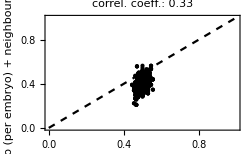

```mathematica
plotNeighbP=Show[Graphics[{Black,Point[{("NumPosCellsICM"/"CellNumberICM"),"MeanRatioPosNeighbPosCell"}/.#]}&/@Select[plotRatiosNSorted,("Stage"/.#)>3&],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion + cells in ICM","mean ratio (per embryo)\n+ neighbours of + cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@("correl. coeff.: "<>ToString[Round[correlP,0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbP_Altern.png"}],plotNeighbP]
```

```mathematica
correlByStageNm=Table [N@Correlation[("NumNegCellsICM"/"CellNumberICM")/.plotRatiosNSortedByStage[[i]],"MeanRatioNegNeighbNegCell"/.plotRatiosNSortedByStage[[i]]],{i,1,3}]
```

{0.312343,0.298213,0.267315}

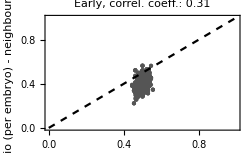
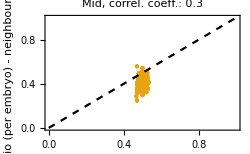
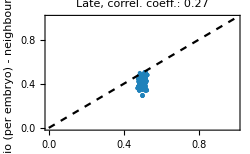

```mathematica
plotNeighbByStageNm=Row[Table[Show[Graphics[{colour3[("Stage"/.#)/.{3.5->1,4.0->2,4.5->3}],Point[{("NumNegCellsICM"/"CellNumberICM"),"MeanRatioNegNeighbNegCell"}/.#]}&/@plotRatiosNSortedByStage[[i]],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion - cells in ICM","mean ratio (per embryo)\n- neighbours of - cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@({"Early, ","Mid, ","Late, "}[[i]]<>"correl. coeff.: "<>ToString[Round[correlByStageNm[[i]],0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbByStageM_Altern.png"}],plotNeighbByStageNm]
```

```mathematica
correlByStageNp=Table [N@Correlation[("NumPosCellsICM"/"CellNumberICM")/.plotRatiosNSortedByStage[[i]],"MeanRatioPosNeighbPosCell"/.plotRatiosNSortedByStage[[i]]],{i,1,3}]
```

{0.390542,0.251958,0.267908}

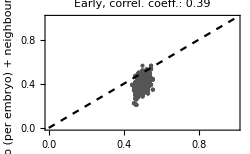
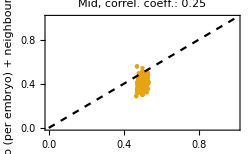
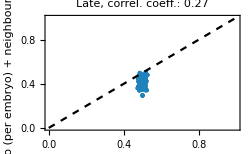

```mathematica
plotNeighbByStageNp=Row[Table[Show[Graphics[{colour3[("Stage"/.#)/.{3.5->1,4.0->2,4.5->3}],Point[{("NumPosCellsICM"/"CellNumberICM"),"MeanRatioPosNeighbPosCell"}/.#]}&/@plotRatiosNSortedByStage[[i]],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion + cells in ICM","mean ratio (per embryo)\n+ neighbours of + cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@({"Early, ","Mid, ","Late, "}[[i]]<>"correl. coeff.: "<>ToString[Round[correlByStageNp[[i]],0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbByStageP_Altern.png"}],plotNeighbByStageNp]
```

### Deterministic models with one realisation

#### Period two I model

```mathematica
nanogNanogComp=Import[FileNameJoin[{baseFolderSimulations,"Results\\nanogNanogCompPeriodTwoI.mx"}]];
```

```mathematica
stages=nanogNanogComp[[All,1,3]];
```

```mathematica
cellNumberPerEmbryo=Length/@nanogNanogComp[[All,2]];
```

```mathematica
plotRatiosNAllCells=calcPlotRatioAllCells["N","N",nanogNanogComp,stages,cellNumberPerEmbryo];
```

```mathematica
plotRatiosNSortedRaw=calcPlotRatioSortedByCellNumber["N","N",nanogNanogComp,stages,cellNumberPerEmbryo];
```

```mathematica
plotRatiosNSorted=Select[plotRatiosNSortedRaw,NumberQ["MeanRatioNegNeighbNegCell"/.#]&&NumberQ["MeanRatioPosNeighbPosCell"/.#]&];
```

```mathematica
Length[plotRatiosNSortedRaw]-Length[plotRatiosNSorted]
```

0

```mathematica
plotRatiosNSortedRawExt=Join[#,{"DiffToLineNegNeigh"->("MeanRatioNegNeighbNegCell"-("NumNegCellsICM"/"CellNumberICM"))/.#,"DiffToLinePosNeigh"->("MeanRatioPosNeighbPosCell"-("NumPosCellsICM"/"CellNumberICM"))/.#}]&/@plotRatiosNSortedRaw;
```

```mathematica
plotRatiosNSortedByStage=Table[Select[plotRatiosNSorted,("Stage"/.#)==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
correlM=N@Correlation[("NumNegCellsICM"/"CellNumberICM")/.Select[plotRatiosNSorted,("Stage"/.#)>3&],"MeanRatioNegNeighbNegCell"/.Select[plotRatiosNSorted,("Stage"/.#)>3&]]
```

0.733344

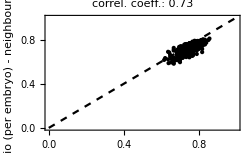

```mathematica
plotNeighbM=Show[Graphics[{Black,Point[{("NumNegCellsICM"/"CellNumberICM"),"MeanRatioNegNeighbNegCell"}/.#]}&/@Select[plotRatiosNSorted,("Stage"/.#)>3&],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion - cells in ICM","mean ratio (per embryo)\n- neighbours of - cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@("correl. coeff.: "<>ToString[Round[correlM,0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbM_PeriodTwoI.png"}],plotNeighbM]
```

the correlation is not defined, becaus one value is always 0

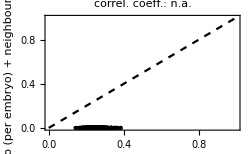

```mathematica
plotNeighbP=Show[Graphics[{Black,Point[{("NumPosCellsICM"/"CellNumberICM"),"MeanRatioPosNeighbPosCell"}/.#]}&/@Select[plotRatiosNSorted,("Stage"/.#)>3&],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion + cells in ICM","mean ratio (per embryo)\n+ neighbours of + cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@("correl. coeff.: "<> "n.a.")],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbP_PeriodTwoI.png"}],plotNeighbP]
```

```mathematica
correlByStageNm=Table [N@Correlation[("NumNegCellsICM"/"CellNumberICM")/.plotRatiosNSortedByStage[[i]],"MeanRatioNegNeighbNegCell"/.plotRatiosNSortedByStage[[i]]],{i,1,3}]
```

{0.69459,0.69144,0.811108}

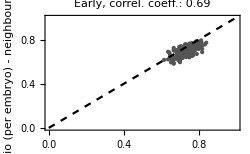
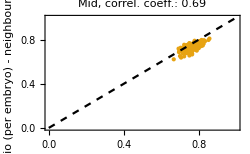
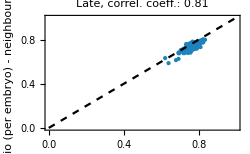

```mathematica
plotNeighbByStageNm=Row[Table[Show[Graphics[{colour3[("Stage"/.#)/.{3.5->1,4.0->2,4.5->3}],Point[{("NumNegCellsICM"/"CellNumberICM"),"MeanRatioNegNeighbNegCell"}/.#]}&/@plotRatiosNSortedByStage[[i]],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion - cells in ICM","mean ratio (per embryo)\n- neighbours of - cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@({"Early, ","Mid, ","Late, "}[[i]]<>"correl. coeff.: "<>ToString[Round[correlByStageNm[[i]],0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbByStageM_PeriodTwoI.png"}],plotNeighbByStageNm]
```

the correlation is not defined, because one value is always 0

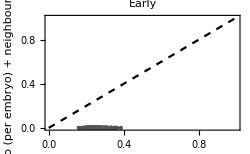
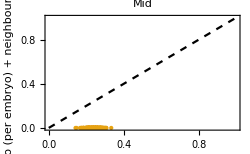
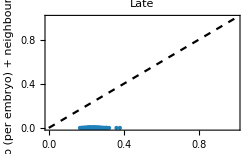

```mathematica
plotNeighbByStageNp=Row[Table[Show[Graphics[{colour3[("Stage"/.#)/.{3.5->1,4.0->2,4.5->3}],Point[{("NumPosCellsICM"/"CellNumberICM"),"MeanRatioPosNeighbPosCell"}/.#]}&/@plotRatiosNSortedByStage[[i]],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion + cells in ICM","mean ratio (per embryo)\n+ neighbours of + cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@({"Early","Mid","Late"}[[i]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbByStageP_PeriodTwoI.png"}],plotNeighbByStageNp]
```

## ODE-based signalling models: ICM composition scatter plots

### Nearest neighbour

```mathematica
(*quadrantsComp=Import[FileNameJoin[{baseFolderSimulations,"Results\\quadrantsCompSimon_ICMCoordinates_with_fates.mx"}]];*)
```

```mathematica
(*cellNumberPerTissue=Length/@quadrantsComp[[All,2]];*)
```

```mathematica
(*plotRatiosSorted=calcPlotRatioSortedByCellNumber["","",quadrantsComp,quadrantsComp[[All,1]],cellNumberPerTissue];*)
```

```mathematica
(*Export[FileNameJoin[{NotebookDirectory[],"ResultsAll","plotRatiosSorted_NN.mx"}],plotRatiosSorted]*)
```

```mathematica
plotRatiosSorted=Import[FileNameJoin[{NotebookDirectory[],"ResultsAll","plotRatiosSorted_NN.mx"}]];
```

```mathematica
plotRatiosSortedCleaned=Select[plotRatiosSorted,NumberQ["MeanRatioNegNeighbNegCell"/.#]&&NumberQ["MeanRatioPosNeighbPosCell"/.#]&];
```

```mathematica
Length[plotRatiosSorted]-Length[plotRatiosSortedCleaned]
```

388

```mathematica
plotRatiosSortedCleanedByStage=Table[Select[plotRatiosSortedCleaned,("Stage"/.("Stage"/.#[[1]]))==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
Length[#]&/@plotRatiosSortedCleanedByStage
```

{32209,21303,16906}

```mathematica
correlP=N@Correlation[("NumPosCellsICM"/"CellNumberICM")/.plotRatiosSortedCleaned,"MeanRatioPosNeighbPosCell"/.plotRatiosSortedCleaned]
```

0.990567

```mathematica
plotNeighbP=Show[Graphics[{Black,Point[{("NumPosCellsICM"/"CellNumberICM"),"MeanRatioPosNeighbPosCell"}/.#]}&/@plotRatiosSortedCleaned,AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion + cells in ICM","mean ratio (per embryo)\n+ neighbours of + cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@("correl. coeff.: "<>ToString[Round[correlP,0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbP_NN.png"}],plotNeighbP]
```

```mathematica
correlN=N@Correlation[("NumNegCellsICM"/"CellNumberICM")/.plotRatiosSortedCleaned,"MeanRatioNegNeighbNegCell"/.plotRatiosSortedCleaned]
```

0.981052

```mathematica
plotNeighbN=Show[Graphics[{Black,Point[{("NumNegCellsICM"/"CellNumberICM"),"MeanRatioNegNeighbNegCell"}/.#]}&/@plotRatiosSortedCleaned,AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion - cells in ICM","mean ratio (per embryo)\n- neighbours of - cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@("correl. coeff.: "<>ToString[Round[correlN,0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbN_NN.png"}],plotNeighbN]
```

```mathematica
correlByStageP=Table [N@Correlation[("NumPosCellsICM"/"CellNumberICM")/.plotRatiosSortedCleanedByStage[[i]],"MeanRatioPosNeighbPosCell"/.plotRatiosSortedCleanedByStage[[i]]],{i,1,3}]
```

{0.989256,0.991575,0.994641}

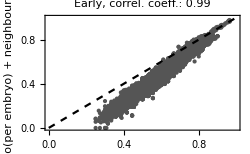
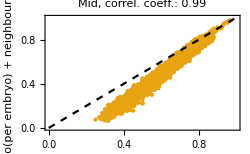
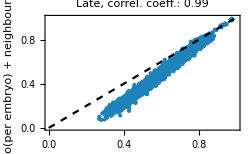

```mathematica
plotNeighbByStageP=Row[Table[Show[Graphics[{colour3[("Stage"/.("Stage"/.#[[1]]))/.{3.5->1,4.0->2,4.5->3}],Point[{("NumPosCellsICM"/"CellNumberICM"),"MeanRatioPosNeighbPosCell"}/.#]}&/@plotRatiosSortedCleanedByStage[[i]],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion + cells in ICM","mean ratio(per embryo)\n+ neighbours of + cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@({"Early, ","Mid, ","Late, "}[[i]]<>"correl. coeff.: "<>ToString[Round[correlByStageP[[i]],0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbByStageP_NN.png"}],plotNeighbByStageP]
```

```mathematica
correlByStageN=Table [N@Correlation[("NumNegCellsICM"/"CellNumberICM")/.plotRatiosSortedCleanedByStage[[i]],"MeanRatioNegNeighbNegCell"/.plotRatiosSortedCleanedByStage[[i]]],{i,1,3}]
```

{0.979599,0.983807,0.989597}

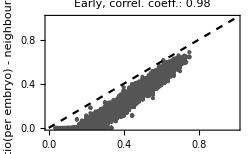
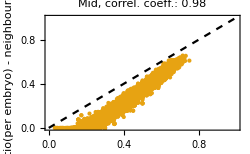
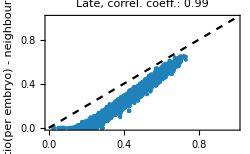

```mathematica
plotNeighbByStageN=Row[Table[Show[Graphics[{colour3[("Stage"/.("Stage"/.#[[1]]))/.{3.5->1,4.0->2,4.5->3}],Point[{("NumNegCellsICM"/"CellNumberICM"),"MeanRatioNegNeighbNegCell"}/.#]}&/@plotRatiosSortedCleanedByStage[[i]],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion - cells in ICM","mean ratio(per embryo)\n- neighbours of - cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@({"Early, ","Mid, ","Late, "}[[i]]<>"correl. coeff.: "<>ToString[Round[correlByStageN[[i]],0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbByStageN_NN.png"}],plotNeighbByStageN]
```

### Distance-based

```mathematica
(*quadrantsComp=Import[FileNameJoin[{baseFolderSimulations,"Results\\quadrantsCompICMCoordinates_globalSignal.mx"}]];*)
```

```mathematica
(*cellNumberPerTissue=Length/@quadrantsComp[[All,2]];*)
```

```mathematica
(*plotRatiosSorted=calcPlotRatioSortedByCellNumber["","",quadrantsComp,quadrantsComp[[All,1]],cellNumberPerTissue];*)
```

```mathematica
(*Export[FileNameJoin[{NotebookDirectory[],"ResultsAll","plotRatiosSorted_DB.mx"}],plotRatiosSorted]*)
```

```mathematica
plotRatiosSorted=Import[FileNameJoin[{NotebookDirectory[],"ResultsAll","plotRatiosSorted_DB.mx"}]];
```

```mathematica
plotRatiosSortedCleaned=Select[plotRatiosSorted,NumberQ["MeanRatioNegNeighbNegCell"/.#]&&NumberQ["MeanRatioPosNeighbPosCell"/.#]&];
```

```mathematica
plotRatiosSortedCleanedByStage=Table[Select[plotRatiosSortedCleaned,("Stage"/.("Stage"/.#[[1]]))==i&],{i,{3.5,4.0,4.5}}];
```

correlation for +

```mathematica
dataByStageP=Table[{"Range_q"/.("Stage"/.#),("NumPosCellsICM"/"CellNumberICM")/.#,"MeanRatioPosNeighbPosCell"/.#}&/@plotRatiosSortedCleanedByStage[[i]],{i,1,3}];
```

```mathematica
dataByStagePBinned=Table[Flatten[#,2]&/@BinLists[dataByStageP[[i]],{0,1,0.1},{-10^6,10^6,2*10^6},{-10^6,10^6,2*10^6}],{i,1,3}];
```

```mathematica
correlByStageP=Table[Table [N@Correlation[dataByStagePBinned[[i]][[j,All,2]],dataByStagePBinned[[i]][[j,All,3]]],{j,1,Length[dataByStagePBinned[[i]]]}],{i,1,3}]
```

{{0.991836,0.991492,0.991685,0.991213,0.990316,0.989642,0.988519,0.987382,0.986377,0.984657},{0.992367,0.992519,0.992735,0.992365,0.992683,0.991774,0.991413,0.990539,0.990008,0.988991},{0.99538,0.994908,0.99443,0.993127,0.992898,0.993248,0.992318,0.992719,0.992089,0.988938}}

```mathematica
Through[{Min,Max}[Flatten[correlByStageP]]]
```

{0.984657,0.99538}

correlation for -

```mathematica
dataByStageN=Table[{"Range_q"/.("Stage"/.#),("NumNegCellsICM"/"CellNumberICM")/.#,"MeanRatioNegNeighbNegCell"/.#}&/@plotRatiosSortedCleanedByStage[[i]],{i,1,3}];
```

```mathematica
dataByStageNBinned=Table[Flatten[#,2]&/@BinLists[dataByStageN[[i]],{0,1,0.1},{-10^6,10^6,2*10^6},{-10^6,10^6,2*10^6}],{i,1,3}];
```

```mathematica
correlByStageN=Table[Table [N@Correlation[dataByStageNBinned[[i]][[j,All,2]],dataByStageNBinned[[i]][[j,All,3]]],{j,1,Length[dataByStageNBinned[[i]]]}],{i,1,3}]
```

{{0.987961,0.983109,0.980179,0.976869,0.975629,0.972109,0.969276,0.96844,0.968178,0.960394},{0.991184,0.987049,0.983548,0.982055,0.982126,0.980526,0.978825,0.98006,0.977519,0.97162},{0.993101,0.988782,0.986734,0.986511,0.986811,0.986639,0.985907,0.985449,0.981974,0.966574}}

```mathematica
Through[{Min,Max}[Flatten[correlByStageN]]]
```

{0.960394,0.993101}

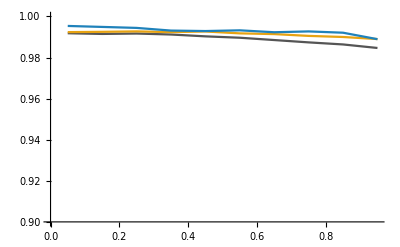

```mathematica
ListLinePlot[Transpose[{Range[0.05,0.95,0.1],#}]&/@correlByStageP,PlotRange->{0.9,1},PlotStyle->colour3/@{1,2,3}]
```

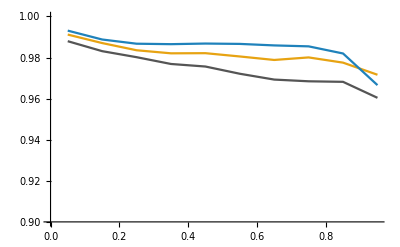

```mathematica
ListLinePlot[Transpose[{Range[0.05,0.95,0.1],#}]&/@correlByStageN,PlotRange->{0.9,1},PlotStyle->colour3/@{1,2,3}]
```

```mathematica
plotNeighbP=Show[Graphics[{ColorData["DarkRainbow"]["Range_q"/.("Stage"/.#[[1]])],Point[{("NumPosCellsICM"/"CellNumberICM"),"MeanRatioPosNeighbPosCell"}/.#]}&/@plotRatiosSortedCleaned,AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion + cells in ICM","mean ratio (per embryo)\n+ neighbours of + cells"})],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbP_DB.png"}],plotNeighbP]
```

```mathematica
plotNeighbN=Show[Graphics[{ColorData["DarkRainbow"]["Range_q"/.("Stage"/.#[[1]])],Point[{("NumNegCellsICM"/"CellNumberICM"),"MeanRatioNegNeighbNegCell"}/.#]}&/@plotRatiosSortedCleaned,AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion - cells in ICM","mean ratio (per embryo)\n- neighbours of - cells"})],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbN_DB.png"}],plotNeighbN]
```

```mathematica
plotNeighbByStageP=Row[Table[Show[Graphics[{ColorData["DarkRainbow"]["Range_q"/.("Stage"/.#[[1]])],Point[{("NumPosCellsICM"/"CellNumberICM"),"MeanRatioPosNeighbPosCell"}/.#]}&/@plotRatiosSortedCleanedByStage[[i]],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion + cells in ICM","mean ratio(per embryo)\n+ neighbours of + cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@({"Early","Mid","Late"}[[i]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbByStageP_DB.png"}],plotNeighbByStageP]
```

```mathematica
plotNeighbByStageN=Row[Table[Show[Graphics[{ColorData["DarkRainbow"]["Range_q"/.("Stage"/.#[[1]])],Point[{("NumNegCellsICM"/"CellNumberICM"),"MeanRatioNegNeighbNegCell"}/.#]}&/@plotRatiosSortedCleanedByStage[[i]],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion - cells in ICM","mean ratio(per embryo)\n- neighbours of - cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@({"Early","Mid","Late"}[[i]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbByStageN_DB.png"}],plotNeighbByStageN]
```

```mathematica
plotDataCleanedq085=Select[plotRatiosSortedCleaned,(0.8<=("Range_q"/.("Stage"/.#))<0.9)&&(("Stage"/.("Stage"/.#))<4.5)&];
```

```mathematica
correlQ085P=N@Correlation[("NumPosCellsICM"/"CellNumberICM")/.#,"MeanRatioPosNeighbPosCell"/.#]&@plotDataCleanedq085
```

0.985194

```mathematica
plotNeighbPQ085=Show[Graphics[{Black,Point[{("NumPosCellsICM"/"CellNumberICM"),"MeanRatioPosNeighbPosCell"}/.#]}&/@plotDataCleanedq085,AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,PlotLabel->Style["correl. coeff.: "<>ToString[Round[correlQ085P,0.01]],14,FontFamily->fontOption,Black],FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion + cells in ICM","mean ratio (per embryo)\n+ neighbours of + cells"})],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbP_DB_q085.png"}],plotNeighbPQ085]
```

```mathematica
correlQ085N=N@Correlation[("NumNegCellsICM"/"CellNumberICM")/.#,"MeanRatioNegNeighbNegCell"/.#]&@plotDataCleanedq085
```

0.967646

```mathematica
plotNeighbNQ085=Show[Graphics[{Black,Point[{("NumNegCellsICM"/"CellNumberICM"),"MeanRatioNegNeighbNegCell"}/.#]}&/@plotDataCleanedq085,AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,PlotLabel->Style["correl. coeff.: "<>ToString[Round[correlQ085N,0.01]],14,FontFamily->fontOption,Black],FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion - cells in ICM","mean ratio (per embryo)\n- neighbours of - cells"})],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbN_DB_q085.png"}],plotNeighbNQ085]
```

### Nearest neighbour with cell division

```mathematica
(*quadrantsComp=Import[FileNameJoin[{baseFolderSimulations,"Results\\quadrantsCompSimonNNSignalCD.mx"}]];*)
```

```mathematica
(*cellNumberPerTissue=Length/@quadrantsComp[[All,2]];*)
```

```mathematica
(*plotRatiosSorted=calcPlotRatioSortedByCellNumber["v","v",quadrantsComp,quadrantsComp[[All,1]],cellNumberPerTissue];*)
```

```mathematica
(*Export[FileNameJoin[{NotebookDirectory[],"ResultsAll","plotRatiosSorted_NNCD.mx"}],plotRatiosSorted]*)
```

```mathematica
plotRatiosSorted=Import[FileNameJoin[{NotebookDirectory[],"ResultsAll","plotRatiosSorted_NNCD.mx"}]];
```

```mathematica
plotRatiosSortedCleaned=Select[plotRatiosSorted,NumberQ["MeanRatioNegNeighbNegCell"/.#]&&NumberQ["MeanRatioPosNeighbPosCell"/.#]&];
```

```mathematica
Length[plotRatiosSorted]-Length[plotRatiosSortedCleaned]
```

18

```mathematica
plotRatiosSortedCleanedByStage=Table[Select[plotRatiosSortedCleaned,("Stage"/.("Stage"/.#[[1]]))==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
Length[#]&/@plotRatiosSortedCleanedByStage
```

{190,196,196}

```mathematica
plotRatiosSortedCleanedByStage[[3,1]]
```

{Stage→{SimulationID→0,Stage→4.5},CellNumberEmbryo→58,CellNumberICM→58,NumPosCellsICM→12,NumNegCellsICM→46,MeanRatioNegNeighbNegCell→35888143/46966920,SEMRatioNegNeighbNegCell→(√(93839614339/70))/2322540,MeanRatioPosNeighbPosCell→45157/308880,SEMRatioPosNeighbPosCell→(√(513054011/11))/308880}

```mathematica
correlP=N@Correlation[("NumPosCellsICM"/"CellNumberICM")/.plotRatiosSortedCleaned,"MeanRatioPosNeighbPosCell"/.plotRatiosSortedCleaned]
```

0.991539

```mathematica
plotNeighbP=Show[Graphics[{Point[{("NumPosCellsICM"/"CellNumberICM"),"MeanRatioPosNeighbPosCell"}/.#]}&/@plotRatiosSortedCleaned,AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,PlotLabel->Style["correl. coeff.: "<>ToString[Round[correlP,0.01]],14,FontFamily->fontOption,Black],FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion + cells in ICM","mean ratio(per embryo)\n+ neighbours of + cells"})],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbP_NNCD.png"}],plotNeighbP]
```

```mathematica
correlN=N@Correlation[("NumNegCellsICM"/"CellNumberICM")/.plotRatiosSortedCleaned,"MeanRatioNegNeighbNegCell"/.plotRatiosSortedCleaned]
```

0.983633

```mathematica
plotNeighbN=Show[Graphics[{Point[{("NumNegCellsICM"/"CellNumberICM"),"MeanRatioNegNeighbNegCell"}/.#]}&/@plotRatiosSortedCleaned,AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,PlotLabel->Style["correl. coeff.: "<>ToString[Round[correlN,0.01]],14,FontFamily->fontOption,Black],FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion - cells in ICM","mean ratio(per embryo)\n- neighbours of - cells"})],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbN_NNCD.png"}],plotNeighbN]
```

```mathematica
correlByStageP=Table [N@Correlation[("NumPosCellsICM"/"CellNumberICM")/.plotRatiosSortedCleanedByStage[[i]],"MeanRatioPosNeighbPosCell"/.plotRatiosSortedCleanedByStage[[i]]],{i,1,3}]
```

{0.990807,0.990003,0.996018}

```mathematica
plotNeighbByStageP=Row[Table[Show[Graphics[{colour3[("Stage"/.("Stage"/.#[[1]]))/.{3.5->1,4.0->2,4.5->3}],Point[{("NumPosCellsICM"/"CellNumberICM"),"MeanRatioPosNeighbPosCell"}/.#]}&/@plotRatiosSortedCleanedByStage[[i]],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion + cells in ICM","mean ratio(per embryo)\n+ neighbours of + cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@({"Early, ","Mid, ","Late, "}[[i]]<>"correl. coeff.: "<>ToString[Round[correlByStageP[[i]],0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbByStageP_NNCD.png"}],plotNeighbByStageP]
```

```mathematica
correlByStageN=Table [N@Correlation[("NumNegCellsICM"/"CellNumberICM")/.plotRatiosSortedCleanedByStage[[i]],"MeanRatioNegNeighbNegCell"/.plotRatiosSortedCleanedByStage[[i]]],{i,1,3}]
```

{0.98251,0.979433,0.99053}

```mathematica
plotNeighbByStageN=Row[Table[Show[Graphics[{colour3[("Stage"/.("Stage"/.#[[1]]))/.{3.5->1,4.0->2,4.5->3}],Point[{("NumNegCellsICM"/"CellNumberICM"),"MeanRatioNegNeighbNegCell"}/.#]}&/@plotRatiosSortedCleanedByStage[[i]],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion - cells in ICM","mean ratio(per embryo)\n- neighbours of - cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@({"Early, ","Mid, ","Late, "}[[i]]<>"correl. coeff.: "<>ToString[Round[correlByStageN[[i]],0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbByStageN_NNCD.png"}],plotNeighbByStageN]
```

### Distance-based with cell division

```mathematica
(*quadrantsComp=Import[FileNameJoin[{baseFolderSimulations,"Results\\quadrantsCompSimonDistSignalCD.mx"}]];*)
```

```mathematica
(*cellNumberPerTissue=Length/@quadrantsComp[[All,2]];*)
```

```mathematica
(*plotRatiosSorted=calcPlotRatioSortedByCellNumber["v","v",quadrantsComp,quadrantsComp[[All,1]],cellNumberPerTissue];*)
```

```mathematica
(*Export[FileNameJoin[{NotebookDirectory[],"ResultsAll","plotRatiosSorted_DBCD.mx"}],plotRatiosSorted]*)
```

```mathematica
plotRatiosSorted=Import[FileNameJoin[{NotebookDirectory[],"ResultsAll","plotRatiosSorted_DBCD.mx"}]];
```

```mathematica
plotRatiosSortedCleaned=Select[plotRatiosSorted,NumberQ["MeanRatioNegNeighbNegCell"/.#]&&NumberQ["MeanRatioPosNeighbPosCell"/.#]&];
```

```mathematica
Length[plotRatiosSorted]-Length[plotRatiosSortedCleaned]
```

257

```mathematica
plotRatiosSortedCleanedByStage=Table[Select[plotRatiosSortedCleaned,("Stage"/.("Stage"/.#[[1]]))==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
neighRatioDistBasedOnICM=Show[Graphics[{ColorData["DarkRainbow"]["Range_q"/.("Stage"/.#[[1]])],Point[{("NumPosCellsICM"/"CellNumberICM"),"MeanRatioPosNeighbPosCell"}/.#]}&/@plotRatiosSortedCleaned,AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion + cells in ICM","mean ratio (per embryo)\n+ neighbours of + cells"})],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighRatioPDistBasedCDOnICM.png"}],neighRatioDistBasedOnICM]
```

```mathematica
plotNeighbByStageP=Row[Table[Show[Graphics[{ColorData["DarkRainbow"]["Range_q"/.("Stage"/.#[[1]])],Point[{("NumPosCellsICM"/"CellNumberICM"),"MeanRatioPosNeighbPosCell"}/.#]}&/@plotRatiosSortedCleanedByStage[[i]],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion + cells in ICM","mean ratio(per embryo)\n+ neighbours of + cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@({"Early","Mid","Late"}[[i]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbByStageP_DBCD.png"}],plotNeighbByStageP]
```

```mathematica
plotNeighbByStageN=Row[Table[Show[Graphics[{ColorData["DarkRainbow"]["Range_q"/.("Stage"/.#[[1]])],Point[{("NumNegCellsICM"/"CellNumberICM"),"MeanRatioNegNeighbNegCell"}/.#]}&/@plotRatiosSortedCleanedByStage[[i]],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion - cells in ICM","mean ratio(per embryo)\n- neighbours of - cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@({"Early","Mid","Late"}[[i]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbByStageN_DBCD.png"}],plotNeighbByStageN]
```

```mathematica
neighRatioDistNBasedOnICM=Show[Graphics[{ColorData["DarkRainbow"]["Range_q"/.("Stage"/.#[[1]])],Point[{("NumNegCellsICM"/"CellNumberICM"),"MeanRatioNegNeighbNegCell"}/.#]}&/@plotRatiosSortedCleaned,AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion - cells in ICM","mean ratio (per embryo)\n- neighbours of - cells"})],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighRatioDistNCDBasedOnICM.png"}],neighRatioDistNBasedOnICM]
```

```mathematica
plotRatiosSortedCleaned[[1]]
```

{Stage→{SimulationID→0,Stage→3.5,Range_q→0.365881},CellNumberEmbryo→22,CellNumberICM→22,NumPosCellsICM→14,NumNegCellsICM→8,MeanRatioNegNeighbNegCell→7/24,SEMRatioNegNeighbNegCell→(√(85/7))/72,MeanRatioPosNeighbPosCell→505697/776160,SEMRatioPosNeighbPosCell→(√(6610854773/13))/776160}

#### bin q<0.1

```mathematica
plotDataCleanedq005=Select[plotRatiosSortedCleaned,(("Range_q"/.("Stage"/.#))<0.1)&&(("Stage"/.("Stage"/.#))<4.5)&];
```

```mathematica
correlQ005P=N@Correlation[("NumPosCellsICM"/"CellNumberICM")/.#,"MeanRatioPosNeighbPosCell"/.#]&@plotDataCleanedq005
```

0.986153

```mathematica
plotNeighbPQ005=Show[Graphics[{Black,Point[{("NumPosCellsICM"/"CellNumberICM"),"MeanRatioPosNeighbPosCell"}/.#]}&/@plotDataCleanedq005,AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,PlotLabel->Style["correl. coeff.: "<>ToString[Round[correlQ005P,0.01]],14,FontFamily->fontOption,Black],FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion + cells in ICM","mean ratio (per embryo)\n+ neighbours of + cells"})],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbVP_DBCD_q005.png"}],plotNeighbPQ005]
```

```mathematica
correlQ005N=N@Correlation[("NumNegCellsICM"/"CellNumberICM")/.#,"MeanRatioNegNeighbNegCell"/.#]&@plotDataCleanedq005
```

0.987879

```mathematica
plotNeighbNQ005=Show[Graphics[{Black,Point[{("NumNegCellsICM"/"CellNumberICM"),"MeanRatioNegNeighbNegCell"}/.#]}&/@plotDataCleanedq005,AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,PlotLabel->Style["correl. coeff.: "<>ToString[Round[correlQ005N,0.01]],14,FontFamily->fontOption,Black],FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion - cells in ICM","mean ratio (per embryo)\n- neighbours of - cells"})],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbN_DBCD_q005.png"}],plotNeighbNQ005]
```

#### bin 0.1<=q<0.2

```mathematica
plotDataCleanedq015=Select[plotRatiosSortedCleaned,(0.1<=("Range_q"/.("Stage"/.#))<0.2)&&(("Stage"/.("Stage"/.#))<4.5)&];
```

```mathematica
correlQ015P=N@Correlation[("NumPosCellsICM"/"CellNumberICM")/.#,"MeanRatioPosNeighbPosCell"/.#]&@plotDataCleanedq015
```

0.987059

```mathematica
plotNeighbPQ015=Show[Graphics[{Black,Point[{("NumPosCellsICM"/"CellNumberICM"),"MeanRatioPosNeighbPosCell"}/.#]}&/@plotDataCleanedq015,AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,PlotLabel->Style["correl. coeff.: "<>ToString[Round[correlQ015P,0.01]],14,FontFamily->fontOption,Black],FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion + cells in ICM","mean ratio (per embryo)\n+ neighbours of + cells"})],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbP_DBCD_q015.png"}],plotNeighbPQ015]
```

```mathematica
correlQ015N=N@Correlation[("NumNegCellsICM"/"CellNumberICM")/.#,"MeanRatioNegNeighbNegCell"/.#]&@plotDataCleanedq015
```

0.987587

```mathematica
plotNeighbNQ015=Show[Graphics[{Black,Point[{("NumNegCellsICM"/"CellNumberICM"),"MeanRatioNegNeighbNegCell"}/.#]}&/@plotDataCleanedq015,AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,PlotLabel->Style["correl. coeff.: "<>ToString[Round[correlQ015N,0.01]],14,FontFamily->fontOption,Black],FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion - cells in ICM","mean ratio (per embryo)\n- neighbours of u+v- cells"})],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbN_DBCD_q015.png"}],plotNeighbNQ015]
```

#### bin 0.4<=q<0.5

```mathematica
plotDataCleanedq045=Select[plotRatiosSortedCleaned,(0.4<=("Range_q"/.("Stage"/.#))<0.5)&&(("Stage"/.("Stage"/.#))<4.5)&];
```

```mathematica
correlQ045P=N@Correlation[("NumPosCellsICM"/"CellNumberICM")/.#,"MeanRatioPosNeighbPosCell"/.#]&@plotDataCleanedq045
```

0.986593

```mathematica
plotNeighbPQ045=Show[Graphics[{Black,Point[{("NumPosCellsICM"/"CellNumberICM"),"MeanRatioPosNeighbPosCell"}/.#]}&/@plotDataCleanedq045,AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,PlotLabel->Style["correl. coeff.: "<>ToString[Round[correlQ045P,0.01]],14,FontFamily->fontOption,Black],FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion + cells in ICM","mean ratio (per embryo)\n+ neighbours of + cells"})],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbP_DBCD_q045.png"}],plotNeighbPQ045]
```

```mathematica
correlQ045N=N@Correlation[("NumNegCellsICM"/"CellNumberICM")/.#,"MeanRatioNegNeighbNegCell"/.#]&@plotDataCleanedq045
```

0.981104

```mathematica
plotNeighbNQ045=Show[Graphics[{Black,Point[{("NumNegCellsICM"/"CellNumberICM"),"MeanRatioNegNeighbNegCell"}/.#]}&/@plotDataCleanedq045,AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,PlotLabel->Style["correl. coeff.: "<>ToString[Round[correlQ045N,0.01]],14,FontFamily->fontOption,Black],FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion - cells in ICM","mean ratio (per embryo)\n- neighbours of u+v- cells"})],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbN_DBCD_q045.png"}],plotNeighbNQ045]
```

#### correlation for v+

```mathematica
dataByStageVp=Table[{"Range_q"/.("Stage"/.#),("NumPosCellsICM"/"CellNumberICM")/.#,"MeanRatioPosNeighbPosCell"/.#}&/@plotRatiosSortedCleanedByStage[[i]],{i,1,3}];
```

```mathematica
dataByStageVpBinned=Table[Flatten[#,2]&/@BinLists[dataByStageVp[[i]],{0,1,0.1},{-10^6,10^6,2*10^6},{-10^6,10^6,2*10^6}],{i,1,3}];
```

```mathematica
correlByStageVp=Table[Table [N@Correlation[dataByStageVpBinned[[i]][[j,All,2]],dataByStageVpBinned[[i]][[j,All,3]]],{j,1,Length[dataByStageVpBinned[[i]]]}],{i,1,3}]
```

{{0.98595,0.984661,0.991361,0.987442,0.987815,0.988797,0.98301,0.982579,0.973173,0.977697},{0.985472,0.989338,0.987995,0.989446,0.98526,0.986865,0.988476,0.98801,0.981553,0.978663},{0.99066,0.988512,0.987957,0.986278,0.990699,0.986718,0.987881,0.985373,0.98256,0.976005}}

```mathematica
Through[{Min,Max}[Flatten[correlByStageVp]]]
```

{0.973173,0.991361}

#### correlation for u+

```mathematica
dataByStageUp=Table[{"Range_q"/.("Stage"/.#),("NumNegCellsICM"/"CellNumberICM")/.#,"MeanRatioNegNeighbNegCell"/.#}&/@plotRatiosSortedCleanedByStage[[i]],{i,1,3}];
```

```mathematica
dataByStageUpBinned=Table[Flatten[#,2]&/@BinLists[dataByStageUp[[i]],{0,1,0.1},{-10^6,10^6,2*10^6},{-10^6,10^6,2*10^6}],{i,1,3}];
```

```mathematica
correlByStageUp=Table[Table [N@Correlation[dataByStageUpBinned[[i]][[j,All,2]],dataByStageUpBinned[[i]][[j,All,3]]],{j,1,Length[dataByStageUpBinned[[i]]]}],{i,1,3}]
```

{{0.991704,0.990428,0.98931,0.987991,0.977418,0.980735,0.96173,0.955097,0.929729,0.919553},{0.984657,0.984907,0.98528,0.990251,0.985289,0.979915,0.972452,0.952284,0.944983,0.904975},{0.994514,0.99235,0.9889,0.984888,0.986321,0.985524,0.983078,0.974993,0.935199,0.929384}}

```mathematica
Through[{Min,Max}[Flatten[correlByStageUp]]]
```

{0.904975,0.994514}

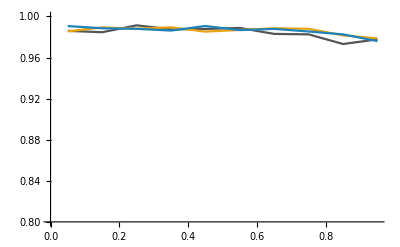

```mathematica
ListLinePlot[Transpose[{Range[0.05,0.95,0.1],#}]&/@correlByStageVp,PlotRange->{0.8,1},PlotStyle->colour3/@{1,2,3}]
```

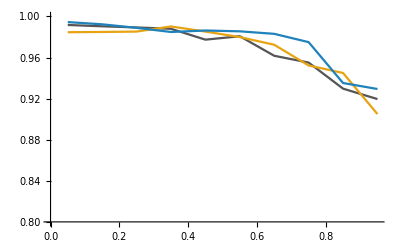

```mathematica
ListLinePlot[Transpose[{Range[0.05,0.95,0.1],#}]&/@correlByStageUp,PlotRange->{0.8,1},PlotStyle->colour3/@{1,2,3}]
```